# Final Project Plots

## Caleb Powell

## Theoretical Equations

```mathematica
Clear[λ,μ]
P0[ρ_]:=(1-ρ)/(1-ρ^11) (*Stationary Distribution*)
P[ρ_,n_]:=P0[ρ]*ρ^n (*Prob of being in state n*)
PBlock[ρ_]:=P[ρ,10](*Blocking Probability*)
L[ρ_]:=∑_(n=0)^10 n*P[ρ,n](*AVG num of Customers*)
B[ρ_]:= 1-P0[ρ](*AVG num of Cust being Served*)
Lq[ρ_]:=(L[ρ]-B[ρ] )(*Avergae Que Length*)
S[ρ_,λ_]:=L[ρ]/λ(*AVG sojourn time*)
S2[ρ_,μ_]:=1/(2μ)*(1-11 ρ^10+10 ρ^11)/((1-ρ)(1-ρ^11))(*AVG sojourn time in terms of μ*)
```

## Strategy 1

## Avg Sojourn Time

### λ Plot (Set μ = 0.5) (λ → {0,1} )

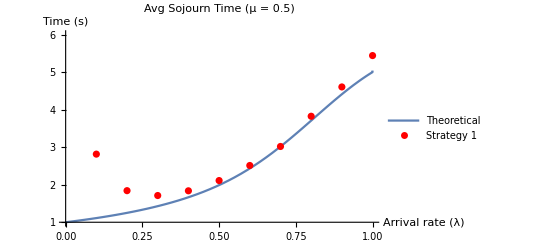

```mathematica
S1x = {0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0};
S1y = ConstantArray[0,11];

S1y[[1]]=Mean[{∞}]; (*λ=0*)
S1y[[2]]=Mean[{2.81358176,2.83475860,2.83207586,2.83291027,2.73862840,2.84147374,2.84258868,2.80004901,2.77923150,2.83119199}];(*λ=0.1*)
S1y[[3]]=Mean[{1.79935562,1.83643982,1.89169390,1.84523658,1.84604295,1.78515374,1.82535414,1.90006331,1.85848296,1.82715428}];(*λ=0.2*)
S1y[[4]]=Mean[{1.74189267,1.77278498,1.70198137,1.69297520,1.70137984,1.65396446,1.71999639,1.81834663,1.62005137,1.69623777}];(*λ=0.3*)
S1y[[5]]=Mean[{1.93578952,1.80708930,1.71258729,1.78679873,1.79012153,1.83269854,1.89686116,1.84274355,1.83322636,1.93842355}];(*λ=0.4*)
S1y[[6]]=Mean[{2.07704372,2.08629478,2.14490980,2.19565977,1.95867324,2.15082653,2.10361202,2.15939524,2.11644579,2.11367681}]; (*λ=0.5*)
S1y[[7]]=Mean[{2.32797589,2.38871560,2.64483769,2.36895260,2.67264764,2.67252411,2.52264919,2.72369338,2.35110069,2.44533339}]; (*λ=0.6*)
S1y[[8]]=Mean[{2.78278393,2.91138933,3.14645367,3.00721159,3.11340963,3.25289972,3.10810542,2.91400409,2.74783930,3.19990098}]; (*λ=0.7*)
S1y[[9]]=Mean[{3.79253325,3.82941603,3.52095384,3.96262679,3.92803821,3.82492114,3.82957452,3.84029596,3.63396139,4.07360015}]; (*λ=0.8*)
S1y[[10]]=Mean[{4.68272912,4.71468203,4.29457237,4.49904664,4.71143118,4.35057620,4.82839938,4.85587240,4.70603549,4.40019867}]; (*λ=0.9*)
S1y[[11]]=Mean[{5.00694663,5.21161105,5.82765637,5.37998847,5.48824024,5.45233759,5.66345786,5.49111459,5.34533339,5.53350439}];(*λ=1.0*)

S1Data = Transpose[{S1x,S1y}];

TheorPlot = Plot[
S2[λ/(2(0.5)),0.5],{λ,0,1},
PlotRange->{1,6},
AxesLabel->{"Arrival rate (λ)","Time (s)"},
PlotLabel->"Avg Sojourn Time (μ  = 0.5)",
PlotLegends->{"Theoretical"}
];

S1Plot = ListPlot[
S1Data ,
PlotStyle->Red,PlotLegends->{"Strategy 1"}
];


Show[{TheorPlot,S1Plot}]
```

### μ Plot (Set λ = 2) (μ → {10,1} )

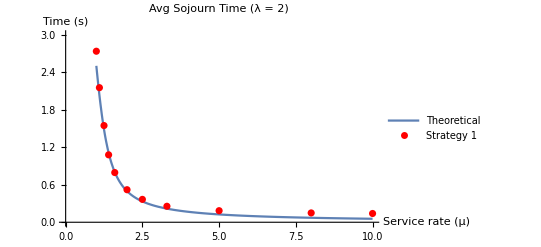

```mathematica
S1x = {1,1.1,1.25,1.4,1.6,2,2.5,3.3,5,8,10};
S1y = ConstantArray[0,11];

S1y[[1]]=Mean[{2.47945363,2.87639322,2.61533687,2.74296000,2.59663451,2.86423400,2.81270753,2.63481124,2.77353385,2.93856173}]; (*μ=1*)
S1y[[2]]=Mean[{1.91427051,2.32821742,2.08951979,2.23466367,2.14155298,2.06456559,2.08516993,2.20123088,2.37264683,2.08008178}];(*μ=1.1*)
S1y[[3]]=Mean[{1.50902266,1.47657369,1.53018057,1.63632230,1.62214962,1.55433074,1.62551482,1.39018691,1.49267871,1.61671383}];(*μ=1.25*)
S1y[[4]]=Mean[{1.17196285,0.98168309,1.04566172,1.06843049,1.05897364,1.15079895,1.04361281,1.13152165,1.04665280,1.07709132}];(*μ=1.4*)
S1y[[5]]=Mean[{0.78380105,0.77689689,0.82865395,0.82181310,0.80788252,0.78340151,0.76923576,0.79497755,0.80933085,0.76781921}];(*μ=1.6*)
S1y[[6]]=Mean[{0.53716975,0.48688136,0.51007501,0.51453857,0.50781391,0.53097685,0.49874113,0.55953013,0.50831632,0.54575677}]; (*μ=2*)
S1y[[7]]=Mean[{0.35821047,0.37328502,0.35951389,0.37253318,0.37311616,0.36688632,0.37343511,0.34445226,0.37611168,0.35803461}]; (*μ=2.5*)
S1y[[8]]=Mean[{0.25720168,0.25801602,0.25718670,0.24688769,0.25866247,0.26941833,0.25414277,0.24737005,0.25908743,0.24684418}]; (*μ=3.3*)
S1y[[9]]=Mean[{0.19624340,0.18036522,0.18160159,0.18666127,0.18023727,0.18327461,0.18557650,0.18271133,0.18586738,0.18434164}]; (*μ=5*)
S1y[[10]]=Mean[{0.14806625,0.14846098,0.14697138,0.14629023,0.14950863,0.15012869,0.15063334,0.15190433,0.14577782,0.15332870}]; (*μ=8*)
S1y[[11]]=Mean[{0.13945912,0.14071287,0.14120501,0.14035143,0.14204008,0.13958869,0.13854743,0.14003991,0.13671653,0.14134506}];(*μ=10*)

S1Data = Transpose[{S1x,S1y}];

TheorPlot = Plot[
S[2/(2μ),2],{μ,1,10},
PlotRange->{0,3},
AxesLabel->{"Service rate (μ)","Time (s)"},
PlotLabel->"Avg Sojourn Time (λ = 2)",
PlotLegends->{"Theoretical"}
];

S1Plot = ListPlot[
S1Data ,
PlotStyle->Red,PlotLegends->{"Strategy 1"}
];


Show[{TheorPlot,S1Plot}]
```

### ρ Plot (Choose and λ,μ such that ρ → {0,1})

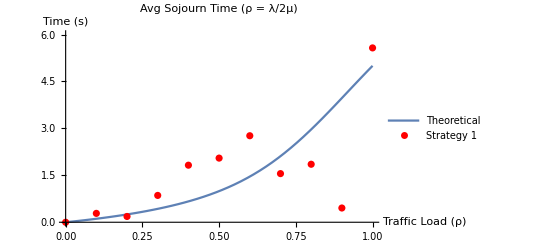

```mathematica
S1x = {0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0};
S1y = ConstantArray[0,11];

S1y[[1]]=Mean[{0}]; (*ρ=0*)
S1y[[2]]=Mean[{0.28877863,0.28468315,0.27838911,0.27861721,0.28868149,0.27727456,0.27777495,0.28767532,0.28745779,0.28936898}];(*ρ=0.1,λ=1.0,μ=5.0*)
S1y[[3]]=Mean[{0.18316606,0.18960587,0.18008322,0.18256329,0.18708501,0.17833909,0.18653338,0.18412281,0.18375039,0.19261620}];(*ρ=0.2,λ=2.0,μ=5.0*)
S1y[[4]]=Mean[{0.84377037,0.83288525,0.83296394,0.84470923,0.86415761,0.88460286,0.87510843,0.85731036,0.90052348,0.84331812}];(*ρ=0.3,λ=0.6,μ=1.0*)
S1y[[5]]=Mean[{1.71193007,1.85751954,1.81377732,1.87219738,1.85940253,1.80063840,1.82651986,1.80110280,1.83535229,1.85993115}];(*ρ=0.4,λ=0.4,μ=0.5*)
S1y[[6]]=Mean[{2.04330393,2.13998829,2.05135746,2.02834871,2.11079550,2.10136919,2.09753555,2.03163919,1.95088093,1.95041476}]; (*ρ=0.5,λ=0.5,μ=0.5*)
S1y[[7]]=Mean[{2.58821640,2.75727858,2.85055339,2.78292460,2.83166435,2.83459755,2.81812472,2.67784667,2.71156561,2.80210976}]; (*ρ=0.6,λ=2,μ=10/6*)
S1y[[8]]=Mean[{1.52001275,1.46701055,1.65812670,1.50252114,1.58295582,1.65498331,1.58776860,1.46853667,1.58061700,1.52620396}]; (*ρ=0.7,λ=1.4,μ=1*)
S1y[[9]]=Mean[{1.83731110,1.92225297,1.79923541,1.86168374,1.88247253,1.85940693,1.73935688,1.85854239,1.93450405,1.84474144}]; (*ρ=0.8,λ=1.6,μ=1.0*)
S1y[[10]]=Mean[{0.47020711,0.43907103,0.48322236,0.52463769,0.42037087,0.41299038,0.46774667,0.43499620,0.46866425,0.43156158}]; (*ρ=0.9,λ=9.0,μ=5.0*)
S1y[[11]]=Mean[{5.46899581,5.44736170,6.04656886,5.54199500,5.58759482,5.35455940,5.12974146,5.87255689,5.60205272,5.67859840}];(*ρ=1.0,λ=1.0,μ=0.5*)

S1Data = Transpose[{S1x,S1y}];

TheorPlot = Plot[
S[ρ,1],{ρ,0,1},
PlotRange->{0,6},
AxesLabel->{"Traffic Load (ρ)","Time (s)"},
PlotLabel->"Avg Sojourn Time (ρ = λ/2μ)",
PlotLegends->{"Theoretical"}
];

S1Plot = ListPlot[
S1Data ,
PlotStyle->Red,PlotLegends->{"Strategy 1"}
];


Show[{TheorPlot,S1Plot}]
```

## Avg Sojourn Time

### λ Plot (Set μ = 0.5) (λ → {0,1} )

```mathematica
S1x = {0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0};
S1y = ConstantArray[0,11];

S1y[[1]]=Mean[{∞}]; (*λ=0*)
S1y[[2]]=Mean[{2.81358176,2.83475860,2.83207586,2.83291027,2.73862840,2.84147374,2.84258868,2.80004901,2.77923150,2.83119199}];(*λ=0.1*)
S1y[[3]]=Mean[{1.79935562,1.83643982,1.89169390,1.84523658,1.84604295,1.78515374,1.82535414,1.90006331,1.85848296,1.82715428}];(*λ=0.2*)
S1y[[4]]=Mean[{1.74189267,1.77278498,1.70198137,1.69297520,1.70137984,1.65396446,1.71999639,1.81834663,1.62005137,1.69623777}];(*λ=0.3*)
S1y[[5]]=Mean[{1.93578952,1.80708930,1.71258729,1.78679873,1.79012153,1.83269854,1.89686116,1.84274355,1.83322636,1.93842355}];(*λ=0.4*)
S1y[[6]]=Mean[{2.07704372,2.08629478,2.14490980,2.19565977,1.95867324,2.15082653,2.10361202,2.15939524,2.11644579,2.11367681}]; (*λ=0.5*)
S1y[[7]]=Mean[{2.32797589,2.38871560,2.64483769,2.36895260,2.67264764,2.67252411,2.52264919,2.72369338,2.35110069,2.44533339}]; (*λ=0.6*)
S1y[[8]]=Mean[{2.78278393,2.91138933,3.14645367,3.00721159,3.11340963,3.25289972,3.10810542,2.91400409,2.74783930,3.19990098}]; (*λ=0.7*)
S1y[[9]]=Mean[{3.79253325,3.82941603,3.52095384,3.96262679,3.92803821,3.82492114,3.82957452,3.84029596,3.63396139,4.07360015}]; (*λ=0.8*)
S1y[[10]]=Mean[{4.68272912,4.71468203,4.29457237,4.49904664,4.71143118,4.35057620,4.82839938,4.85587240,4.70603549,4.40019867}]; (*λ=0.9*)
S1y[[11]]=Mean[{5.00694663,5.21161105,5.82765637,5.37998847,5.48824024,5.45233759,5.66345786,5.49111459,5.34533339,5.53350439}];(*λ=1.0*)

S1Data = Transpose[{S1x,S1y}];

TheorPlot = Plot[
S2[λ/(2(0.5)),0.5],{λ,0,1},
PlotRange->{1,6},
AxesLabel->{"Arrival rate (λ)","Time (s)"},
PlotLabel->"Avg Sojourn Time (μ  = 0.5)",
PlotLegends->{"Theoretical"}
];

S1Plot = ListPlot[
S1Data ,
PlotStyle->Red,PlotLegends->{"Strategy 1"}
];


Show[{TheorPlot,S1Plot}]
```

-Graphics-

### μ Plot (Set λ = 2) (μ → {10,1} )

```mathematica
S1x = {1,1.1,1.25,1.4,1.6,2,2.5,3.3,5,8,10};
S1y = ConstantArray[0,11];

S1y[[1]]=Mean[{2.47945363,2.87639322,2.61533687,2.74296000,2.59663451,2.86423400,2.81270753,2.63481124,2.77353385,2.93856173}]; (*μ=1*)
S1y[[2]]=Mean[{1.91427051,2.32821742,2.08951979,2.23466367,2.14155298,2.06456559,2.08516993,2.20123088,2.37264683,2.08008178}];(*μ=1.1*)
S1y[[3]]=Mean[{1.50902266,1.47657369,1.53018057,1.63632230,1.62214962,1.55433074,1.62551482,1.39018691,1.49267871,1.61671383}];(*μ=1.25*)
S1y[[4]]=Mean[{1.17196285,0.98168309,1.04566172,1.06843049,1.05897364,1.15079895,1.04361281,1.13152165,1.04665280,1.07709132}];(*μ=1.4*)
S1y[[5]]=Mean[{0.78380105,0.77689689,0.82865395,0.82181310,0.80788252,0.78340151,0.76923576,0.79497755,0.80933085,0.76781921}];(*μ=1.6*)
S1y[[6]]=Mean[{0.53716975,0.48688136,0.51007501,0.51453857,0.50781391,0.53097685,0.49874113,0.55953013,0.50831632,0.54575677}]; (*μ=2*)
S1y[[7]]=Mean[{0.35821047,0.37328502,0.35951389,0.37253318,0.37311616,0.36688632,0.37343511,0.34445226,0.37611168,0.35803461}]; (*μ=2.5*)
S1y[[8]]=Mean[{0.25720168,0.25801602,0.25718670,0.24688769,0.25866247,0.26941833,0.25414277,0.24737005,0.25908743,0.24684418}]; (*μ=3.3*)
S1y[[9]]=Mean[{0.19624340,0.18036522,0.18160159,0.18666127,0.18023727,0.18327461,0.18557650,0.18271133,0.18586738,0.18434164}]; (*μ=5*)
S1y[[10]]=Mean[{0.14806625,0.14846098,0.14697138,0.14629023,0.14950863,0.15012869,0.15063334,0.15190433,0.14577782,0.15332870}]; (*μ=8*)
S1y[[11]]=Mean[{0.13945912,0.14071287,0.14120501,0.14035143,0.14204008,0.13958869,0.13854743,0.14003991,0.13671653,0.14134506}];(*μ=10*)

S1Data = Transpose[{S1x,S1y}];

TheorPlot = Plot[
S[2/(2μ),2],{μ,1,10},
PlotRange->{0,3},
AxesLabel->{"Service rate (μ)","Time (s)"},
PlotLabel->"Avg Sojourn Time (λ = 2)",
PlotLegends->{"Theoretical"}
];

S1Plot = ListPlot[
S1Data ,
PlotStyle->Red,PlotLegends->{"Strategy 1"}
];


Show[{TheorPlot,S1Plot}]
```

-Graphics-

### ρ Plot (Choose and λ,μ such that ρ → {0,1})

```mathematica
S1x = {0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0};
S1y = ConstantArray[0,11];

S1y[[1]]=Mean[{0}]; (*ρ=0*)
S1y[[2]]=Mean[{0.28877863,0.28468315,0.27838911,0.27861721,0.28868149,0.27727456,0.27777495,0.28767532,0.28745779,0.28936898}];(*ρ=0.1,λ=1.0,μ=5.0*)
S1y[[3]]=Mean[{0.18316606,0.18960587,0.18008322,0.18256329,0.18708501,0.17833909,0.18653338,0.18412281,0.18375039,0.19261620}];(*ρ=0.2,λ=2.0,μ=5.0*)
S1y[[4]]=Mean[{0.84377037,0.83288525,0.83296394,0.84470923,0.86415761,0.88460286,0.87510843,0.85731036,0.90052348,0.84331812}];(*ρ=0.3,λ=0.6,μ=1.0*)
S1y[[5]]=Mean[{1.71193007,1.85751954,1.81377732,1.87219738,1.85940253,1.80063840,1.82651986,1.80110280,1.83535229,1.85993115}];(*ρ=0.4,λ=0.4,μ=0.5*)
S1y[[6]]=Mean[{2.04330393,2.13998829,2.05135746,2.02834871,2.11079550,2.10136919,2.09753555,2.03163919,1.95088093,1.95041476}]; (*ρ=0.5,λ=0.5,μ=0.5*)
S1y[[7]]=Mean[{2.58821640,2.75727858,2.85055339,2.78292460,2.83166435,2.83459755,2.81812472,2.67784667,2.71156561,2.80210976}]; (*ρ=0.6,λ=2,μ=10/6*)
S1y[[8]]=Mean[{1.52001275,1.46701055,1.65812670,1.50252114,1.58295582,1.65498331,1.58776860,1.46853667,1.58061700,1.52620396}]; (*ρ=0.7,λ=1.4,μ=1*)
S1y[[9]]=Mean[{1.83731110,1.92225297,1.79923541,1.86168374,1.88247253,1.85940693,1.73935688,1.85854239,1.93450405,1.84474144}]; (*ρ=0.8,λ=1.6,μ=1.0*)
S1y[[10]]=Mean[{0.47020711,0.43907103,0.48322236,0.52463769,0.42037087,0.41299038,0.46774667,0.43499620,0.46866425,0.43156158}]; (*ρ=0.9,λ=9.0,μ=5.0*)
S1y[[11]]=Mean[{5.46899581,5.44736170,6.04656886,5.54199500,5.58759482,5.35455940,5.12974146,5.87255689,5.60205272,5.67859840}];(*ρ=1.0,λ=1.0,μ=0.5*)

S1Data = Transpose[{S1x,S1y}];

TheorPlot = Plot[
S[ρ,1],{ρ,0,1},
PlotRange->{0,6},
AxesLabel->{"Traffic Load (ρ)","Time (s)"},
PlotLabel->"Avg Sojourn Time (ρ = λ/2μ)",
PlotLegends->{"Theoretical"}
];

S1Plot = ListPlot[
S1Data ,
PlotStyle->Red,PlotLegends->{"Strategy 1"}
];


Show[{TheorPlot,S1Plot}]
```

-Graphics-